```mathematica
Clear["Global`*"]
```

```mathematica
r=0.64;
l=1.5;
mc=0.3;
oc=0.15;
margin=0.03;
os=0.009;
ms=0.006;
β=π/12;
mrc=mc/3;
orc=oc/4;
mmrc=orc;
cm={0,0.04};
m=1;
maxγ=π/3;
g=9.82;
CSm=50/1000;
bodym=(450-260)/1000;
servom=6/1000;
batterym=265/1000;
electronicsm=(320-260)/1000;
electronicscm={0,0.04};
bodycm={0,mc/2-0.14};
batterycm={0,mc/2-0.02};
motorm=38/1000;
motorcm={-0.2,mc/2};
eservocm={-0.05,0};
rservocm={-0.6,0};
propellerm=12/1000;
propellercm={0,0.02}+motorcm;
```

```mathematica
θ=ArcTan[-(-mc/2+ms-(-oc/2+os)),l/2-margin];
α=αx/.Solve[{Sin[θ]Sin[αx]-Cos[αx]Cos[maxγ]Cos[θ]==0,π>αx>0},αx][[1]];
R=Sin[θ]/Sin[-β+θ]*mmrc;
eL=Norm[{l/2-margin,-oc/2+os}*r+{0,-mc/2+ms}*(1-r)-{0,-mc/2+ms}];
rL=Norm[{l/2-margin,-oc/2+os}*r+{0,-mc/2+ms}*(1-r)-{l/2-margin,-oc/2+os}];
```

```mathematica
R
```

0.0399835

```mathematica
eCS={{0,-mc/2+ms},
{0,-mc/2+ms}+{Cos[θ+α],-Sin[θ+α]}*mrc/Cos[α],
{l/2-margin,-oc/2+os}*r+{0,-mc/2+ms}*(1-r)+{Cos[θ+β],-Sin[θ+β]}*R,
{l/2-margin,-oc/2+os}*r+{0,-mc/2+ms}*(1-r)};
rCS={{l/2-margin,-oc/2+os}*r+{0,-mc/2+ms}*(1-r),
{l/2-margin,-oc/2+os}*r+{0,-mc/2+ms}*(1-r)+{Cos[θ-β],-Sin[θ-β]}*mmrc/Cos[β],
{l/2-margin,-oc/2+os}+{Cos[θ+β],-Sin[θ+β]}*orc/Cos[β],
{l/2-margin,-oc/2+os}};
```

```mathematica
wing=Reverse[{{0,-mc/2+ms},{-l/2+margin,-oc/2+os},
{0,-mc/2}*margin/l*2+{-l/2,-oc/2}*(1-margin/l*2),
{-l/2,-oc/2},{-l/2,oc/2},{0,mc/2},{l/2,oc/2},{l/2,-oc/2},{0,-mc/2}*margin/l*2+{l/2,-oc/2}*(1-margin/l*2),{l/2-margin,-oc/2+os},{0,-mc/2+ms}
}];
```

```mathematica
Area[n_List]:=Total[Det/@Partition[n,2,1,{1,1}]]/2
CenterOfMass[n_List]:=Module[{x,y,m,det,dx,dy},m=Partition[n,2,1,{1,1}];
det=Det/@m;
dx=Last[#]+First[#]&/@m[[All,All,1]];
dy=Last[#]+First[#]&/@m[[All,All,2]];
x=Total[det dx];
y=Total[det dy];
1/(6Area[n]){x,y}]
```

```mathematica
flip[p_]:={{-1,0},{0,1}}.p
```

```mathematica
eA=Area[eCS];
rA=Area[rCS];
wA=Area[wing];
tA=wA+2rA+2eA;
ecm=CenterOfMass[eCS];
rcm=CenterOfMass[rCS];
```

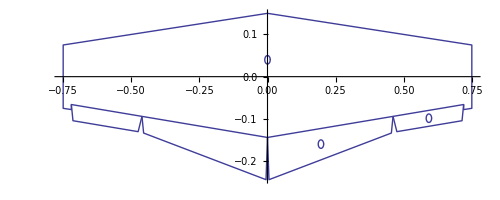

```mathematica
Show[
ListLinePlot[wing],
ListLinePlot[Table[flip[i],{i,eCS}]],
ListLinePlot[Table[flip[i],{i,rCS}]],
ListLinePlot[eCS],
ListLinePlot[rCS],
ListLinePlot[Table[ecm+0.01*{Cos[2π i/100],Sin[2π i/100]},{i,0,101}]],
ListLinePlot[Table[rcm+0.01*{Cos[2π i/100],Sin[2π i/100]},{i,0,101}]],
ListLinePlot[Table[cm+0.01*{Cos[2π i/100],Sin[2π i/100]},{i,0,101}]],
AspectRatio->Automatic,PlotRange->All
]
```

```mathematica
p={flip[rcm],flip[ecm], ecm, rcm};
A={rA,eA,eA,rA};
```

```mathematica
erM=Transpose[Table[(p[[j]]-cm)*A[[j]],{j,1,4}]];
```

```mathematica
nv=NullSpace[erM];
```

```mathematica
nv4=Table[Normalize[i]*Sign[Total[i]],{i,{nv[[1]]-nv[[2]]nv[[1]][[4]]/nv[[2]][[4]],
       nv[[2]]-nv[[1]]nv[[2]][[1]]/nv[[1]][[1]]}}];
```

```mathematica
sym=Normalize[nv4[[1]]+nv4[[2]]];
asym=Normalize[nv4[[1]]-nv4[[2]]];
```

```mathematica
skew=nv4[[1]];
brake=sym;
pitch=Normalize[({1,1,1,1}-t*sym)/.Minimize[
({1,1,1,1}-t*sym).DiagonalMatrix[A].({1,1,1,1}-t*sym)
,t][[2]][[1]]];
roll=Normalize[({-1,-1,1,1}-t*asym)/.Minimize[
({-1,-1,1,1}-t*asym).DiagonalMatrix[A].({-1,-1,1,1}-t*asym)
,t][[2]][[1]]];
```

```mathematica
Grid[{{"","CS 1","CS 2","CS 3","CS 4"},{"skew"}~Join~skew,{"brake"}~Join~brake,{"pitch"}~Join~pitch,{"roll"}~Join~roll},Frame->All]
```

| CS 1 | CS 2 | CS 3 | CS 4
skew | 0.838708 | -0.46146 | 0.289178 | 0.
brake | 0.692645 | -0.142279 | -0.142279 | 0.692645
pitch | 0.402761 | 0.581192 | 0.581192 | 0.402761
roll | -0.67125 | -0.222314 | 0.222314 | 0.67125

```mathematica
Grid[{{"Outer CS area","Inner CS area","Total CS area"},{2rA,2eA,2rA+2eA}/tA},Frame->All]
```

Outer CS area | Inner CS area | Total CS area
0.0462187 | 0.155925 | 0.202143

```mathematica
Grid[{{"Outer length","Outer width","Inner length","Inner width"},{rL,orc,eL,mrc}},Frame->All]
```

Outer length | Outer width | Inner length | Inner width
0.260717 | 0.0375 | 0.463496 | 0.1

```mathematica
skewEffiency=-skew.DiagonalMatrix[A*Transpose[p][[1]]].skew/
(skew.skew)
```

0.0047217

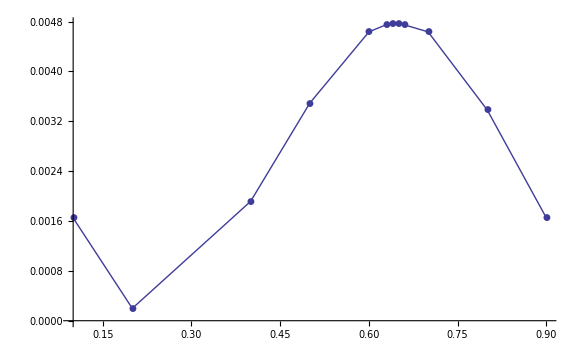

```mathematica
ListLinePlot[{{0.1,0.0016495198397913826},{0.2,0.0001980694287184984},{0.4,0.0019152542579542044},{0.5,0.0034911129021768673},{0.6,0.004635749333239049},{0.63,0.00475333205141244},{0.64,0.004765191360971644},{0.65,0.0047634088890852674},{0.66,0.004748168115114836},{0.7,0.004635749333239049},{0.8,0.0033829341649519603},{0.9,0.0016495198397913826}},PlotMarkers->Automatic]
```

```mathematica
getx[ru_,pu_,sm_]:=x/.NSolve[-(x skew+ru roll+pu pitch).DiagonalMatrix[A*Transpose[p][[1]]].(x skew+ru roll+pu pitch)==sm,x,Reals][[2]]
```

```mathematica
getx[rx_,px_,sx_]:=(rx roll+px pitch+t1 sym+t2 asym)/.Minimize[{(rx roll+px pitch+t1 sym+t2 asym).DiagonalMatrix[A].(rx roll+px pitch+t1 sym+t2 asym),

(rx roll+px pitch+t1 sym+t2 asym).DiagonalMatrix[A*Transpose[p][[1]]].(rx roll+px pitch+t1 sym+t2 asym)+sx==0},{t1,t2}][[2]]
```

```mathematica
Manipulate[BarChart[getx[r,p,s],PlotRange->{-2,2}],
{{s,0},-0.01,0.01},{{r,0},-1,1},{{p,0},-1,1},{{b,0},0,1}
]
```

```mathematica
10Tan[β]//N
```

2.67949

```mathematica
(10-100orc)Tan[β]//N
```

1.67468

```mathematica
10Tan[α]//N
```

0.541667

```mathematica
0.1 Tan[α]+eL//N
```

0.468913

```mathematica
25.8+10Tan[α]//N
```

26.3417

```mathematica
27.3+10Tan[β]//N
```

29.9795

```mathematica
eL+rL
```

0.724213

```mathematica
rm=CSm rA/(2rA+2eA);
```

```mathematica
em=CSm eA/(2rA+2eA);
```

```mathematica
masses={bodym,batterym,servom,servom,servom,servom,rm,rm,em,em,electronicsm,motorm, motorm,propellerm,propellerm};
```

```mathematica
cms={bodycm,batterycm,rservocm,flip[rservocm],eservocm,flip[eservocm],rcm,flip[rcm],ecm,flip[ecm],electronicscm,motorcm,flip[motorcm],propellercm,flip[propellercm]};
```

```mathematica
cm=masses .cms
```

{0.,0.0469431}

```mathematica
totalm=Total[masses]//N
```

0.689

```mathematica
Sqrt[totalm g/(0.5 tA 1.2)]
```

5.26524

```mathematica
PieChart[{bodym,batterym,4servom,CSm,electronicsm,2 motorm+2propellerm},ChartLabels->{"body","battery","servos","control\n surfaces","electronics","motors"}]
```

-Graphics-

```mathematica
relP[p_]:=(p-cm)~Join~{0};
```

```mathematica
BT=Sum[masses[[i]](relP[cms[[i]]].relP[cms[[i]]]*IdentityMatrix[3]-KroneckerProduct[relP[cms[[i]]],relP[cms[[i]]]]),{i,1,Length[masses]}]+{{0.04^2+((oc+mc)/2)^2,0,0},{0,0.04^2+l^2,0},{0,0,l^2+((oc+mc)/2)^2}}*bodym/12;
```

```mathematica
BT//MatrixForm
```

(0.00603014 | 0. | 0.
0. | 0.0494968 | 0.
0. | 0. | 0.0554763)